```mathematica
Clear["Global`*"];
a:=2;
Remove[ffund,orthDeriv];
ffund:=Log[(##[[1]]^2+##[[2]]^2)^(1/2)]&;
orthDeriv[f_,xy_]:={-D[f[{x,y}],y],D[f[{x,y}],x]}/.{x->xy[[1]],y->xy[[2]]};
e1:={1,0};
f1:=ffund[##-e1]+ffund[##+e1]&;
g1:=orthDeriv[f1,##] &;
Remove[x,y];
```

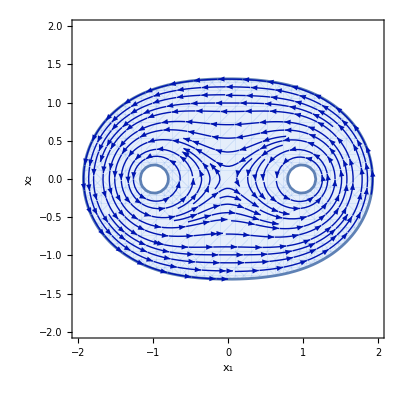

```mathematica
StreamPlot[g1[{x,y}],{x,-a,a},{y,-a,a}, StreamPoints->Fine,FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, RegionFunction->Function[{x,y,vx,vy,n},-1<f1[{x,y}]<1]]
```

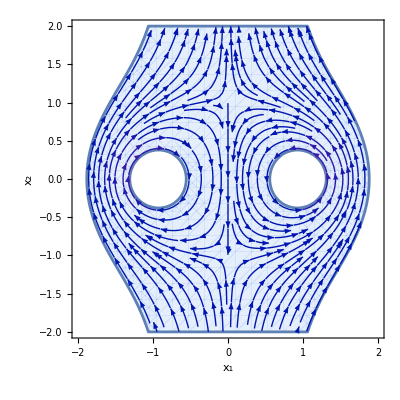

```mathematica
f2:=ffund[##-e1]-ffund[##+e1]+##[[1]]&;
g2:=orthDeriv[f2,##] &
StreamPlot[g2[{x,y}],{x,-a,a},{y,-a,a},StreamPoints->Fine,FrameLabel->{Subscript[x, 1],Subscript[x, 2]},RegionFunction->Function[{x,y,vx,vy,n},-0.7<f2[{x,y}]<0.7 && -2<y<2]]
```

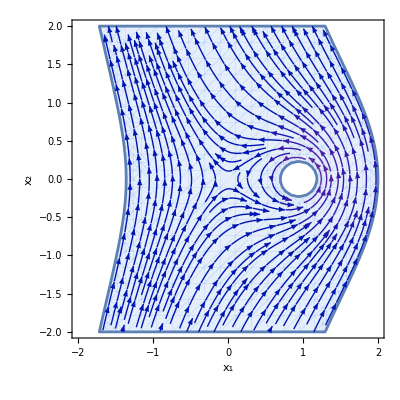

```mathematica
f3:=ffund[##-e1]+##[[1]]&;
g3:=orthDeriv[f3,##] &
StreamPlot[g3[{x,y}],{x,-a,a},{y,-a,a},StreamPoints->Fine,FrameLabel->{Subscript[x, 1],Subscript[x, 2]},RegionFunction->Function[{x,y,vx,vy,n},-0.5<f3[{x,y}]<2 && -2<y<2]]
```

```mathematica
Animate[StreamPlot[(1-lambda)*g1[{x,y}]+lambda*g2[{x,y}],{x,-a,a},{y,-a,a},FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, StreamPoints->Fine],{lambda,0,1},AnimationRunning->False, AnimationRate->.05]
```

```mathematica
Animate[VectorPlot[(1-lambda)*g1[{x,y}]4+lambda*g2[{x,y}],{x,-a,a},{y,-a,a},FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, VectorPoints->Fine],{lambda,0,1},AnimationRunning->False, AnimationRate->.05]
```

```mathematica
regionOmega=RegionDifference[Disk[{0,0},4],RegionUnion[Disk[{-2,0},1],Disk[{2,0},1]]];
solveDirichlet[uBoundary_]:=Module[{uval},
LaplaceEquation2D={Laplacian[u[x,y],{x,y}]==0, DirichletCondition[u[x,y]==uBoundary[x,y],True]};
(*Dsolve[LaplaceEquation2D, u[x,y],x,y]*)
uval=NDSolveValue[LaplaceEquation2D,u,{x,y}∈regionOmega][##[[1]],##[[2]]]&;uval]
uBoundary=If[#1^2+#2^2>15,0,1]&;
f4 = solveDirichlet[uBoundary];
g4:=orthDeriv[f4,##]&;
```

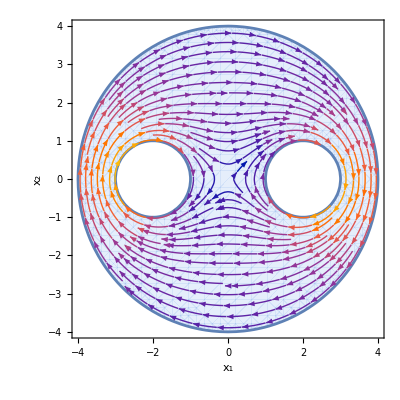

```mathematica
StreamPlot[Evaluate[g4[{x,y}]],{x,y}∈regionOmega,FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, StreamPoints->Fine]
```

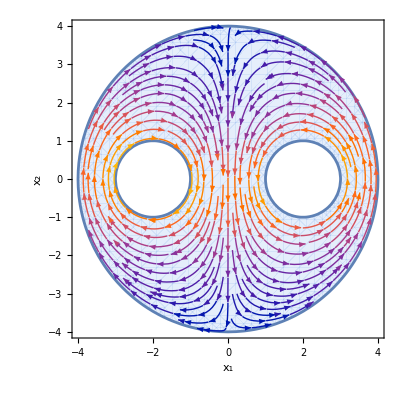

```mathematica
uBoundary=If[#1^2+#2^2>15,0,If[#1>0,-1,1]]&;
f5 = solveDirichlet[uBoundary];
g5:=orthDeriv[f5,##]&;
StreamPlot[Evaluate[g5[{x,y}]],{x,y}∈regionOmega,FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, StreamPoints->Fine]
```

```mathematica
Animate[StreamPlot[Evaluate[(1-lambda)*g4[{x,y}]+lambda*g5[{x,y}]],{x,y}∈regionOmega,FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, StreamPoints->Fine],{lambda,0,1},AnimationRunning->False, AnimationRate->.05]
```